# Practical 4 Solution of Differential Equation by Variation of Parameter method

Rule for solving y’’+p(x)y’+q(x)y=r(x) by using variation parameter(with constant coefficients)

```mathematica
(*Given y''[x]+p y'[x]+q y[x]==r[x]...(!)*)
yh=DSolve[y''[x]+p y'[x]+q y[x]==0,y[x],x]
```

```mathematica
(*....(2)*)(*solution of associated homogeneous ODE*)
```

{{y[x]→ⅇ^(1/2 (-p-√(p^2-4 q)) x) C[1]+ⅇ^(1/2 (-p+√(p^2-4 q)) x) C[2]}}

```mathematica
rule={u''[x]+p u'[x]+q u[x]->0,v''[x]+p v'[x]+q v[x]->0}
```

```mathematica
(*u=e^(1/2(-p-sqrt[p^2-4 q])x) and v=e^(1/2(-p+sqrt[p^2-4 q])x) are Linearly Independent Solution of associated homogeneous ODE*)
```

{q u[x]+p u'[x]+u''[x]→0,q v[x]+p v'[x]+v''[x]→0}

```mathematica
y[x_]:=C1[x]u[x]+C2[x]v[x](*...(3)*)(*yh is solution o eq(2) where C[1]=C1[x] and C[2]= C2[x]*)
first =D[y[x],x]
```

u[x] C1'[x]+v[x] C2'[x]+C1[x] u'[x]+C2[x] v'[x]

```mathematica
rule1={C1'[x]u[x]+C2'[x]v[x]->0}(*...(4)*)
```

{u[x] C1'[x]+v[x] C2'[x]→0}

```mathematica
output1=first/.rule1(*...(5)*)(*give y'*)
```

C1[x] u'[x]+C2[x] v'[x]

```mathematica
second=D[output1,x](*...(6)*)(*gives y''*)
```

C1'[x] u'[x]+C2'[x] v'[x]+C1[x] u''[x]+C2[x] v''[x]

```mathematica
third={second+p(output1)+q(y[x])==r[x]}//Simplify(*using eqn 3,5,and 6 in 1*)
```

{C1'[x] u'[x]+C2'[x] v'[x]+C1[x] (q u[x]+p u'[x]+u''[x])+C2[x] (q v[x]+p v'[x]+v''[x])==r[x]}

```mathematica
output2=third/.rule//Simplify(*...(7)*)
```

{r[x]==C1'[x] u'[x]+C2'[x] v'[x]}

```mathematica
DSolve[{u[x]C1'[x]+v[x]C2'[x]==0,r[x]==C1'[x]u'[x]+C2'[x]v'[x]},{C1[x],C2[x]},x]
```

```mathematica
(*From eqn(4) and (7)*)(*After using the value of C1[x] and C2[x] in eqn(3),
```

```mathematica
we get required solution in the form of y=yc+yp*)
```

{{C1[x]→C[1]+Integrate[(r[K[1]] v[K[1]])/(v[K[1]] u'[K[1]]-u[K[1]] v'[K[1]]),{K[1],1,x},Assumptions→True],C2[x]→C[2]+Integrate[(r[K[2]] u[K[2]])/(-v[K[2]] u'[K[2]]+u[K[2]] v'[K[2]]),{K[2],1,x},Assumptions→True]}}

Solve  y’’+y=cosec(x) by variation of parameters

```mathematica
Clear[y,x]
```

```mathematica
yh=DSolve[y''[x]+y[x]==0,y[x],x](*Solution of associated Homogeneous ODE*)
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
u[x_]:=Cos[x]
```

```mathematica
v[x_]:=Sin[x](*we supposed*)
```

```mathematica
r[x_]:=Csc[x]
```

```mathematica
wronskian=Det[{{u[x],v[x]},{u'[x],v'[x]}}]//Simplify(*Wronskian*)
```

1

```mathematica
C1prime=-v[x]r[x]/wronskian(*=C1'[x]*)
```

-1

```mathematica
C2prime=u[x]r[x]/wronskian
```

Cot[x]

```mathematica
C1[x_]:=Integrate[C1prime,x]+c1
C2[x_]:=Integrate[C2prime,x]+c2
y=C1[x]u[x]+C2[x]v[x](*Required General solution*)
```

(c1-x) Cos[x]+(c2+Log[Sin[x]]) Sin[x]

```mathematica
(*General solution of the given ODE is y=yc+yp where yc=c1 Cos[x]+c2 Sin[x],
yp=-x Cos[x]+Sin[x] Log[Sin[x]]*)
```

```mathematica
DSolve[y''[x]+y[x]==Csc[x],y[x],x]//TraditionalForm(*Verified directly*)
```

{{y(x)→c_2 sin(x)+c_1 cos(x)-x cos(x)+sin(x) log(sin(x))}}

(Alternative)Solve y’’+y=tan(x) by variation of parameter

```mathematica
Clear[y,x]
```

```mathematica
yc=DSolve[y''[x]+y[x]==0,y[x],x](*Solution of associated Homogeneous ODE*)
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
u[x_]:=Cos[x]
```

```mathematica
v[x_]:=Sin[x](*we Supposed*)
```

```mathematica
r[x_]:=Tan[x]
```

```mathematica
wronskian=Det[{{u[x],v[x]},{u'[x],v'[x]}}]//Simplify(*Wronskian*)
```

1

```mathematica
C1prime=-v[x]r[x]/wronskian(*=C1'[x]*)
```

-Sin[x] Tan[x]

```mathematica
C2prime=u[x] r[x]/wronskian
```

Sin[x]

```mathematica
C1[x_]:=Integrate[C1prime,x]
```

```mathematica
C2[x_]:=Integrate[C2prime,x]
```

```mathematica
yp=C1[x] u[x]+C2[x] v[x](*Required General solution*)
```

-Cos[x] Sin[x]+Cos[x] (Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+Sin[x])

```mathematica
(*General solution of the given ODE is y=yc+yp where yc=C[1] Cos[x]+C[2]Sin[x],
yp=-x Cos[x]+Sin[x] Log[Sin[x]]*)
```

```mathematica
sol=Evaluate[y[x]/.yc]+yp
```

{C[1] Cos[x]+C[2] Sin[x]-Cos[x] Sin[x]+Cos[x] (Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+Sin[x])}

```mathematica
tab=Table[sol/.{C[1]->i,C[2]->j},{i,-1,0},{j,0,1}]//Flatten
```

{-Cos[x]-Cos[x] Sin[x]+Cos[x] (Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+Sin[x]),-Cos[x]+Sin[x]-Cos[x] Sin[x]+Cos[x] (Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+Sin[x]),-Cos[x] Sin[x]+Cos[x] (Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+Sin[x]),Sin[x]-Cos[x] Sin[x]+Cos[x] (Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+Sin[x])}

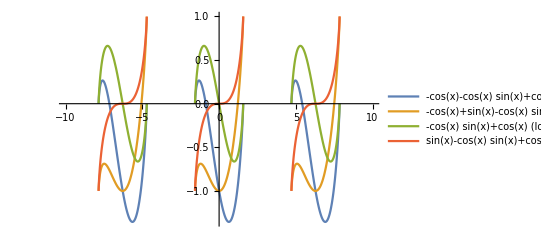

```mathematica
Plot[Evaluate[tab],{x,-10,10},PlotLegends->"Expressions"]
```

```mathematica
Clear[y,x]
```

```mathematica
DSolve[y''[x]+y[x]==Tan[x],y[x],x](*Verfied directly*)
```

{{y[x]→C[1] Cos[x]+Cos[x] Log[Cos[x/2]-Sin[x/2]]-Cos[x] Log[Cos[x/2]+Sin[x/2]]+C[2] Sin[x]}}